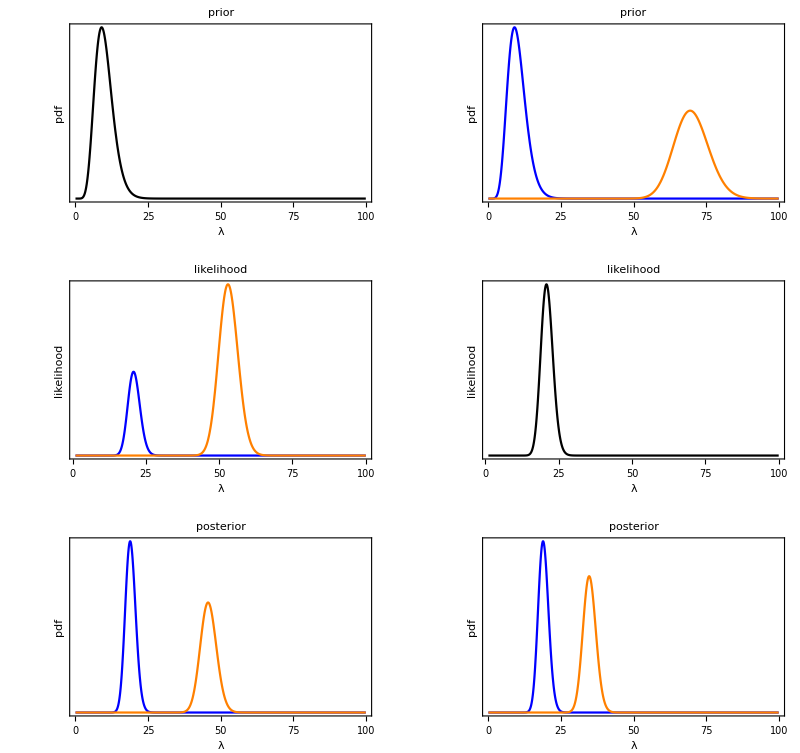

```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"]
α = 10;
β = 1;
y1 = {10,25,19,40,10};
y2 = {40,45,55,60,65};
{α1,β1} = {α,β};
{α2,β2} = {140,2};
fCustomGammaDistribution[α_,β_]:=GammaDistribution[α,1/β]
gPrior1 = Plot[PDF[fCustomGammaDistribution[α,β], x],{x,0,100},Frame->{True,True,False,False},FrameLabel->{"λ","pdf"},PlotStyle->Black,PlotRange->Full,BaseStyle->{FontSize->16},FrameTicks->{True,None},PlotLabel->"prior"];
gLikelihood1 = Plot[{Likelihood[PoissonDistribution[λ],y1],Likelihood[PoissonDistribution[λ],y2]/1000},{λ,1,100},Frame->{True,True,False,False},FrameLabel->{"λ","likelihood "},PlotStyle->{Blue,Orange,Green},PlotRange->Full,BaseStyle->{FontSize->16},FrameTicks->{True,None},PlotLabel->"likelihood"];
gPosterior1 = Plot[{PDF[fCustomGammaDistribution[α+Total@y1,β + 5], x],PDF[fCustomGammaDistribution[α+Total@y2,β + 5], x]},{x,0,100},Frame->{True,True,False,False},FrameLabel->{"λ","pdf"},PlotStyle->{Blue,Orange,Green},PlotRange->Full,BaseStyle->{FontSize->16},FrameTicks->{True,None},PlotLabel->"posterior"];
gPrior2 = Plot[{PDF[fCustomGammaDistribution[α1,β1], x],PDF[fCustomGammaDistribution[α2,β2], x]},{x,0,100},PlotStyle->{Blue,Orange,Green},Frame->{True,True,False,False},FrameLabel->{"λ","pdf"},PlotStyle->Black,PlotRange->Full,BaseStyle->{FontSize->16},FrameTicks->{True,None},PlotLabel->"prior"];
gLikelihood2 =Plot[Likelihood[PoissonDistribution[λ],y1],{λ,1,100},Frame->{True,True,False,False},FrameLabel->{"λ","likelihood "},PlotStyle->Black,PlotRange->Full,BaseStyle->{FontSize->16},FrameTicks->{True,None},PlotLabel->"likelihood"];
gPosterior2 = Plot[{PDF[fCustomGammaDistribution[α1+Total@y1,β1 + 5], x],PDF[fCustomGammaDistribution[α2+Total@y1,β2+ 5], x]},{x,0,100},Frame->{True,True,False,False},FrameLabel->{"λ","pdf"},PlotStyle->{Blue,Orange,Green},PlotRange->Full,BaseStyle->{FontSize->16},FrameTicks->{True,None},PlotLabel->"posterior"];
gFinal=Show[GraphicsGrid[{{gPrior1,gPrior2},{gLikelihood1,gLikelihood2},{gPosterior1,gPosterior2}}],ImageSize->800]
```

```mathematica
Export["Conjugate_poissonGamma.pdf",gFinal]
```

Conjugate_poissonGamma.pdf